```mathematica
Подключаем необходимые пакеты
```

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
Начиная с 9-й версии Mathematica пакет VectorAnalysis можно не подключать
```

```mathematica
Задаём значения констант
```

```mathematica
ϵ=0.001;X0={-1,-2};α=1;
```

```mathematica
Определяем необходимые функции
```

```mathematica
f[{x_,y_}]:=α(x^2-y)^2+(x-1)^2
```

```mathematica
Начиная с 9-й версии Mathematica антиградиент функции двух переменных определяем слудющим образом
```

```mathematica
antiGradF[{x1_,x2_}]:=-Grad[f[{x,y}],{x,y}]/.{x->x1,y->x2}
```

```mathematica
В более ранних версиях эту функцию следует определять следующим образом
```

```mathematica
antiGradF[{x1_,x2_}]:=-Grad[f[{x,y}],Cartesian[x,y,z]][[1;;2]]/.{x->x1,y->x2}
```

```mathematica
NormGradF[{x_,y_}]:=Norm[antiGradF[{x,y}]]
```

```mathematica
uniformMesh[left_,right_,n_]:=Table[i,{i,left,right,(right-left)/n}]
```

```mathematica
Инициализируем переменные
```

```mathematica
X=X0;
points={X0};
norm={NormGradF[X0]};
κArray={1};fValues={f[X0]};
```

```mathematica
shownorm:=Dynamic[ListLogPlot[norm,PlotStyle->{Blue,Thick,PointSize[Large]},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k итерация","||w^k||"},ImageSize->700,Joined->True,Mesh->Full,MeshStyle->Directive[PointSize[0.02],Red],PlotRange->{ϵ/10,2norm[[1]]},Epilog->{Thickness[0.004],Purple,Line[{{1,Log[ϵ]},{Length[norm],Log[ϵ]}}],Text[Style["ϵ",FontSize->24,Black],{1+0.05(Length[norm]-1),Log[2ϵ]}]}]];
```

```mathematica
АЛГОРИТМ
```

```mathematica
shownorm
While[norm[[-1]]≥ϵ,
κArray=Append[κArray,NArgMin[f[X+κ antiGradF[X]],κ]];
X+=κArray[[-1]] antiGradF[X];
points=Append[points,X];
fValues=Append[fValues,f[X]];
norm=Append[norm,NormGradF[X]]
(*Print[ToString[it]<>": норма градиента = "<>ToString[Round[norm[[-1]],0.01ϵ]]];*)
];"Результат получен за "<>ToString[Length[points]-1]<> " итер.: X = "<>ToString[X]
```

Результат получен за 97 итер.: X = {0.999308, 0.99819}

```mathematica
CP0={-3,-3};num=9;
Manipulate[ContourPlot[f[{x,y}],{x,CP0[[1]],3},{y,CP0[[2]],3},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;4]]~Join~{fValues[[8]],fValues[[20]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],LabelStyle->Large,FrameStyle->Thick,ImageSize->500,PlotPoints->100,Epilog->{Purple,Thickness[0.008],Table[Arrow[points[[i-1;;i]]],{i,2,num}],Darker[Red],PointSize[0.03],Point[points[[1;;num]]],Black,Point[points[[-1]]]}],{num,1,Length[points],1}]
```

Part::partd: Part specification fValues ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification fValues ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 4 in fValues.

Join::heads: Heads uniformMesh and Part at positions 1 and 2 are expected to be the same.

Part::take: Cannot take positions 1 through 2 in points.

Part::take: Cannot take positions 2 through 3 in points.

General::stop: Further output of Part :: take will be suppressed during this calculation.

Join::heads: Heads uniformMesh and Part at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

ContourPlot::plln: Limiting value CP0 ⟦ 1 ⟧ in {x, CP0 ⟦ 1 ⟧, 3} is not a machine-sized real number.

Part::partd: Part specification fValues ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification fValues ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 4 in fValues.

Join::heads: Heads uniformMesh and Part at positions 1 and 2 are expected to be the same.

Part::take: Cannot take positions 1 through 2 in points.

Part::take: Cannot take positions 2 through 3 in points.

General::stop: Further output of Part :: take will be suppressed during this calculation.

Join::heads: Heads uniformMesh and Part at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

ContourPlot::plln: Limiting value CP0 ⟦ 1 ⟧ in {x, CP0 ⟦ 1 ⟧, 3} is not a machine-sized real number.

```mathematica
Далее приведены примеры оформления результатов вычислительного эксперимента для представления их в курсовых работах / отчетах и т.д.
```

```mathematica
Поскольку представленные выше анимации являются динамическими объектами, для возможности быстрого сравнения результатов расчета разными методами, нужно построить и графики из пп. 2-3 , (а также таблицу, см. п. 4).
```

```mathematica
АНАЛИЗ РЕЗУЛЬТАТОВ ВЫЧИСЛИТЕЛЬНОГО ЭКСПЕРИМЕНТА
```

```mathematica
1. Топография целевой функции
```

```mathematica
Пример ''нечитабельного графика'': линии уровня сливаются
```

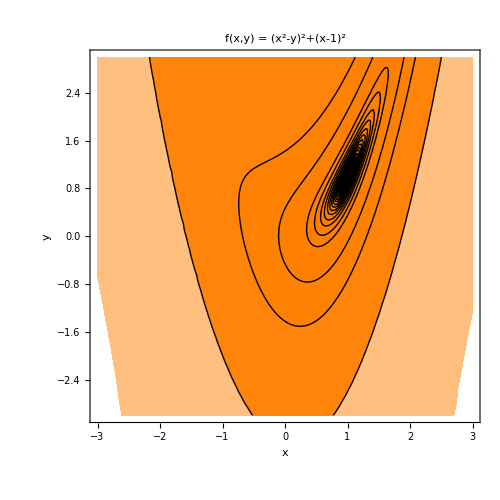

```mathematica
ContourPlot[f[{x,y}],{x,-3,3},{y,-3,3},Contours->fValues,ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],LabelStyle->Large,FrameStyle->Thick,ImageSize->500]
```

```mathematica
Как лучше построить график:
```

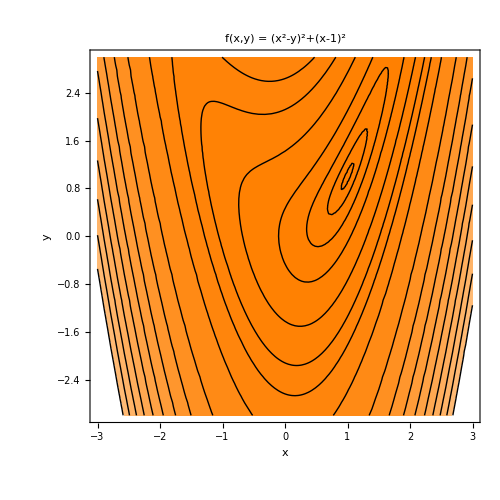

```mathematica
CP0={-3,-3};
ContourPlot[f[{x,y}],{x,CP0[[1]],3},{y,CP0[[2]],3},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;4]]~Join~{fValues[[8]],fValues[[20]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],LabelStyle->Large,FrameStyle->Thick,ImageSize->500]
```

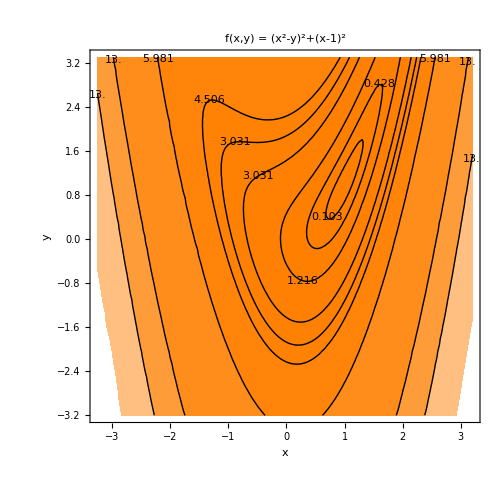

```mathematica
CP0={-3,-3};
ContourPlot[f[{x,y}],{x,CP0[[1]]-0.25,3.2},{y,CP0[[2]]-0.2,3.3},Contours->uniformMesh[fValues[[1]],0.55(f[CP0]-fValues[[1]]),2]~Join~uniformMesh[fValues[[2]],0.6(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;4]]~Join~{fValues[[8]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],LabelStyle->Large,FrameStyle->Thick,ImageSize->500,ContourLabels->Function[{x,y,z},Text[Framed[Style[Round[z,ϵ],FontSize->16]],{x,y},Background->White]]]
```

```mathematica
2. Траектория поиска точки минимума
```

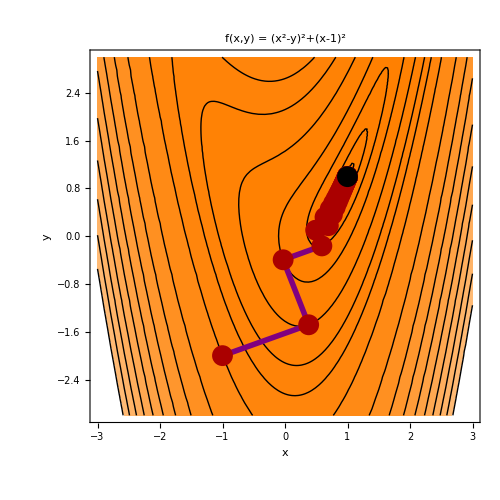

```mathematica
CP0={-3,-3};
ContourPlot[f[{x,y}],{x,CP0[[1]],3},{y,CP0[[2]],3},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;4]]~Join~{fValues[[8]],fValues[[20]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],LabelStyle->Large,FrameStyle->Thick,ImageSize->500,Epilog->{Purple,Thickness[0.008],Line[points],Darker[Red],PointSize[0.03],Point[points],Black,Point[points[[len]]]}]
```

```mathematica
В случае медленносходящегося метода лучше строить только начальный участок траектории и последнюю её точку
```

```mathematica
CP0={-3,-3};num=9;
ContourPlot[f[{x,y}],{x,CP0[[1]],3},{y,CP0[[2]],3},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;4]]~Join~{fValues[[8]],fValues[[20]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],LabelStyle->Large,FrameStyle->Thick,ImageSize->500,PlotPoints->100,Epilog->{Purple,Thickness[0.008],Table[Arrow[points[[i-1;;i]]],{i,2,num}],Darker[Red],PointSize[0.03],Point[points[[1;;num]]],Black,Point[points[[-1]]]}]
```

-Graphics-

```mathematica
Сохраняем графики в *.pdf или, если есть русскоязычные подписи, в *.tiff. *.tiff можно импортировать в Mathematica при помощи функции Import[] и сохранить в *.pdf.
Переход в текущий каталог: SetDirectory[NotebookDirectory[]]
```

```mathematica
3. Анализ сходимости метода: убывание нормы невязки
```

```mathematica
''Нечитабельный'' график
```

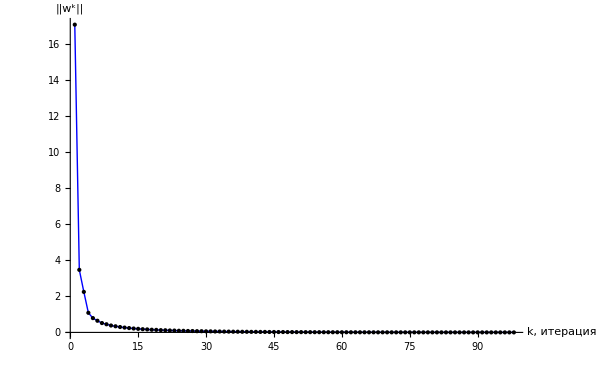

```mathematica
ListLinePlot[norm,PlotRange->All,Mesh->Full,MeshStyle->PointSize[Large],PlotStyle->{Blue,Thick},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","||w^k||"},ImageSize->600]
```

```mathematica
График убывания нормы невязки лучше строить в логарифмическом масштабе
```

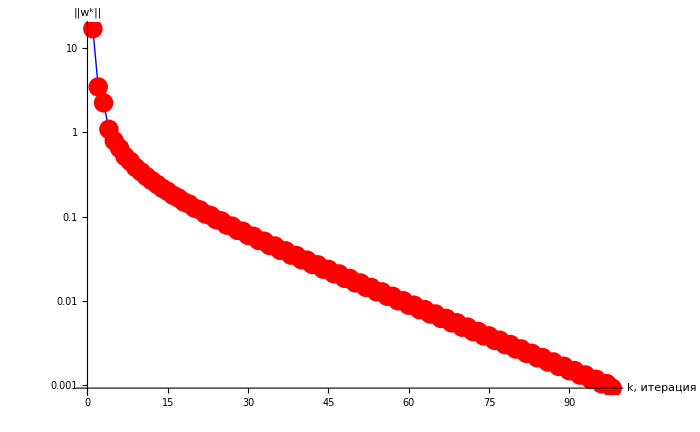

```mathematica
ListLogPlot[norm,PlotRange->All,PlotStyle->{Blue,Thick,PointSize[Large]},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","||w^k||"},ImageSize->700,Joined->True,Mesh->Full,MeshStyle->Directive[PointSize[0.02],Red]]
```

```mathematica
4. Таблицы
```

```mathematica
gridLabel={"k","X^k","f(X^k)","κ_k","||w^k||"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,Length[points]}];gridData[[All,1]]=Table[i,{i,0,Length[points]-1}];
For[i=1,i≤Length[points],i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],8]]<>", "<>ToString[SetAccuracy[points[[i,2]],8]]<>" )"]
gridData[[All,3]]=SetAccuracy[fValues,8];
gridData[[All,4]]=SetAccuracy[κArray,8];
gridData[[All,5]]=SetAccuracy[norm,8];
gridData={gridLabel}~Join~gridData;
```

```mathematica
Grid[gridData,Frame->All,FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15]]
```

k | X^k | f(X^k) | κ_k | ||w^k||
0 | ( -1.0000000, -2.0000000 ) | 13. | 1. | 17.088007
1 | ( 0.3785555, -1.4830417 ) | 3.0311944 | 0.0861597 | 3.4738764
2 | ( -0.0297935, -0.3941112 ) | 1.2164987 | 0.3347782 | 2.2499144
3 | ( 0.5898576, -0.1617421 ) | 0.4279844 | 0.294139 | 1.0886642
4 | ( 0.4910751, 0.1016780 ) | 0.2784583 | 0.2584201 | 0.7944596
5 | ( 0.6933118, 0.1775168 ) | 0.1859663 | 0.2718689 | 0.6475595
6 | ( 0.6403056, 0.3188666 ) | 0.1376838 | 0.233124 | 0.5190464
7 | ( 0.7582230, 0.3630856 ) | 0.1033224 | 0.2426292 | 0.4524402
8 | ( 0.7233731, 0.4560186 ) | 0.081045 | 0.2193716 | 0.3830561
9 | ( 0.8034786, 0.4860582 ) | 0.0640672 | 0.2233426 | 0.3407342
10 | ( 0.7782878, 0.5532337 ) | 0.0519124 | 0.2105557 | 0.2990294
11 | ( 0.8370720, 0.5752778 ) | 0.0422736 | 0.2099514 | 0.2678797
12 | ( 0.8178489, 0.6265395 ) | 0.0349715 | 0.2043732 | 0.2411541
13 | ( 0.8630484, 0.6434892 ) | 0.0290303 | 0.2001751 | 0.2165121
14 | ( 0.8478601, 0.6839914 ) | 0.0243628 | 0.1997869 | 0.1986503
15 | ( 0.8837137, 0.6974365 ) | 0.020497 | 0.192759 | 0.1783847
16 | ( 0.8714214, 0.7302159 ) | 0.0173827 | 0.1962524 | 0.166092
17 | ( 0.9004981, 0.7411196 ) | 0.0147695 | 0.1869681 | 0.1490441
18 | ( 0.8903741, 0.7681167 ) | 0.0126254 | 0.1934526 | 0.1404027
19 | ( 0.9143457, 0.7771061 ) | 0.0108085 | 0.1823442 | 0.1258573
20 | ( 0.9058968, 0.7996365 ) | 0.0092969 | 0.191189 | 0.1196867
21 | ( 0.9259103, 0.8071416 ) | 0.0080061 | 0.1785872 | 0.1071596
22 | ( 0.9187866, 0.8261383 ) | 0.0069207 | 0.1893297 | 0.1027014
23 | ( 0.9356623, 0.8324667 ) | 0.0059881 | 0.1754918 | 0.091842
24 | ( 0.9296067, 0.8486150 ) | 0.0051971 | 0.1877834 | 0.0885929
25 | ( 0.9439501, 0.8539938 ) | 0.0045141 | 0.1729124 | 0.0791345
26 | ( 0.9387685, 0.8678116 ) | 0.0039309 | 0.1864844 | 0.0767516
27 | ( 0.9510389, 0.8724130 ) | 0.0034252 | 0.1707431 | 0.0684844
28 | ( 0.9465810, 0.8843005 ) | 0.0029908 | 0.1853842 | 0.0667294
29 | ( 0.9571343, 0.8882580 ) | 0.002613 | 0.1689047 | 0.0594835
30 | ( 0.9532820, 0.8985310 ) | 0.0022869 | 0.1844461 | 0.0581878
31 | ( 0.9623989, 0.9019498 ) | 0.0020025 | 0.1673366 | 0.0518235
32 | ( 0.9590573, 0.9108608 ) | 0.001756 | 0.1836417 | 0.050866
33 | ( 0.9669631, 0.9138255 ) | 0.0015405 | 0.1659918 | 0.0452664
34 | ( 0.9640553, 0.9215796 ) | 0.0013532 | 0.1829487 | 0.0445596
35 | ( 0.9709325, 0.9241586 ) | 0.0011891 | 0.1648332 | 0.0396257
36 | ( 0.9683954, 0.9309242 ) | 0.001046 | 0.1823492 | 0.0391054
37 | ( 0.9743942, 0.9331738 ) | 0.0009204 | 0.1638311 | 0.0347532
38 | ( 0.9721754, 0.9390905 ) | 0.0008106 | 0.1818288 | 0.0343719
39 | ( 0.9774200, 0.9410573 ) | 0.0007141 | 0.1629614 | 0.030529
40 | ( 0.9754758, 0.9462419 ) | 0.0006296 | 0.1813758 | 0.0302516
41 | ( 0.9800703, 0.9479649 ) | 0.0005553 | 0.1622045 | 0.0268556
42 | ( 0.9783637, 0.9525158 ) | 0.00049 | 0.1809804 | 0.0266558
43 | ( 0.9823956, 0.9540277 ) | 0.0004325 | 0.1615439 | 0.0236528
44 | ( 0.9808954, 0.9580282 ) | 0.000382 | 0.1806346 | 0.023511
45 | ( 0.9844390, 0.9593570 ) | 0.0003375 | 0.1609663 | 0.0208538
46 | ( 0.9831185, 0.9628782 ) | 0.0002983 | 0.1803316 | 0.0207552
47 | ( 0.9862369, 0.9640476 ) | 0.0002637 | 0.1604603 | 0.0184029
48 | ( 0.9850733, 0.9671503 ) | 0.0002332 | 0.1800656 | 0.0183364
49 | ( 0.9878206, 0.9681805 ) | 0.0002062 | 0.1600161 | 0.016253
50 | ( 0.9867944, 0.9709172 ) | 0.0001825 | 0.1798317 | 0.0162102
51 | ( 0.9892172, 0.9718258 ) | 0.0001615 | 0.1596258 | 0.0143642
52 | ( 0.9883112, 0.9742417 ) | 0.000143 | 0.1796259 | 0.0143388
53 | ( 0.9904497, 0.9750436 ) | 0.0001266 | 0.1592823 | 0.0127028
54 | ( 0.9896493, 0.9771780 ) | 0.0001121 | 0.1794446 | 0.01269
55 | ( 0.9915383, 0.9778863 ) | 0.0000993 | 0.1589797 | 0.0112396
56 | ( 0.9908308, 0.9797731 ) | 0.000088 | 0.1792846 | 0.0112358
57 | ( 0.9925005, 0.9803993 ) | 0.0000779 | 0.1587128 | 0.0099496
58 | ( 0.9918747, 0.9820682 ) | 0.0000691 | 0.1791434 | 0.0099522
59 | ( 0.9933515, 0.9826220 ) | 0.0000612 | 0.1584773 | 0.0088114
60 | ( 0.9927976, 0.9840989 ) | 0.0000543 | 0.1790187 | 0.0088183
61 | ( 0.9941044, 0.9845890 ) | 0.0000481 | 0.1582693 | 0.0078062
62 | ( 0.9936140, 0.9858966 ) | 0.0000427 | 0.1789085 | 0.0078159
63 | ( 0.9947709, 0.9863305 ) | 0.0000378 | 0.1580854 | 0.0069179
64 | ( 0.9943366, 0.9874887 ) | 0.0000336 | 0.178811 | 0.0069294
65 | ( 0.9953612, 0.9878730 ) | 0.0000298 | 0.1579228 | 0.0061325
66 | ( 0.9949764, 0.9888992 ) | 0.0000264 | 0.1787247 | 0.0061449
67 | ( 0.9958842, 0.9892396 ) | 0.0000234 | 0.1577789 | 0.0054376
68 | ( 0.9955431, 0.9901492 ) | 0.0000208 | 0.1786483 | 0.0054504
69 | ( 0.9963477, 0.9904509 ) | 0.0000184 | 0.1576516 | 0.0048225
70 | ( 0.9960453, 0.9912573 ) | 0.0000164 | 0.1785805 | 0.0048352
71 | ( 0.9967585, 0.9915248 ) | 0.0000145 | 0.1575388 | 0.0042779
72 | ( 0.9964904, 0.9922398 ) | 0.0000129 | 0.1785206 | 0.0042902
73 | ( 0.9971228, 0.9924770 ) | 0.0000114 | 0.157439 | 0.0037954
74 | ( 0.9968850, 0.9931112 ) | 0.0000102 | 0.1784672 | 0.0038072
75 | ( 0.9974459, 0.9933216 ) | 9.×10^-6 | 0.1573505 | 0.0033679
76 | ( 0.9972349, 0.9938842 ) | 8.×10^-6 | 0.1784201 | 0.003379
77 | ( 0.9977325, 0.9940708 ) | 7.1×10^-6 | 0.157272 | 0.0029889
78 | ( 0.9975453, 0.9945700 ) | 6.3×10^-6 | 0.1783784 | 0.0029993
79 | ( 0.9979868, 0.9947356 ) | 5.6×10^-6 | 0.1572024 | 0.0026529
80 | ( 0.9978206, 0.9951786 ) | 5.×10^-6 | 0.1783414 | 0.0026626
81 | ( 0.9982124, 0.9953255 ) | 4.4×10^-6 | 0.1571406 | 0.0023549
82 | ( 0.9980649, 0.9957186 ) | 3.9×10^-6 | 0.1783085 | 0.0023638
83 | ( 0.9984126, 0.9958490 ) | 3.5×10^-6 | 0.1570858 | 0.0020906
84 | ( 0.9982818, 0.9961980 ) | 3.1×10^-6 | 0.1782794 | 0.0020988
85 | ( 0.9985904, 0.9963137 ) | 2.7×10^-6 | 0.1570372 | 0.0018561
86 | ( 0.9984742, 0.9966235 ) | 2.4×10^-6 | 0.1782535 | 0.0018636
87 | ( 0.9987481, 0.9967263 ) | 2.2×10^-6 | 0.1569941 | 0.0016481
88 | ( 0.9986450, 0.9970013 ) | 1.9×10^-6 | 0.1782305 | 0.0016548
89 | ( 0.9988882, 0.9970925 ) | 1.7×10^-6 | 0.1569559 | 0.0014634
90 | ( 0.9987966, 0.9973367 ) | 1.5×10^-6 | 0.1782102 | 0.0014696
91 | ( 0.9990125, 0.9974177 ) | 1.3×10^-6 | 0.1569219 | 0.0012996
92 | ( 0.9989312, 0.9976345 ) | 1.2×10^-6 | 0.1781921 | 0.0013051
93 | ( 0.9991230, 0.9977064 ) | 1.1×10^-6 | 0.1568917 | 0.0011541
94 | ( 0.9990508, 0.9978989 ) | 9.×10^-7 | 0.178176 | 0.0011591
95 | ( 0.9992210, 0.9979628 ) | 8.×10^-7 | 0.156865 | 0.001025
96 | ( 0.9991569, 0.9981337 ) | 7.×10^-7 | 0.1781618 | 0.0010295
97 | ( 0.9993081, 0.9981904 ) | 7.×10^-7 | 0.1568413 | 0.0009103

```mathematica
Для методов с медленной сходимостью лучше представлять в таблице данные с первых и с последних итераций
```

```mathematica
Grid[gridData[[1;;10]]~Join~{Table["...",{i,1,Length[gridLabel]}]}~Join~gridData[[len-4;;len+1]],Frame->All,FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15]]
```

k | X^k | f(X^k) | κ_k | ||w^k||
0 | ( -1.0000000, -2.0000000 ) | 13. | 1. | 17.088007
1 | ( 0.3785555, -1.4830417 ) | 3.0311944 | 0.0861597 | 3.4738764
2 | ( -0.0297935, -0.3941112 ) | 1.2164987 | 0.3347782 | 2.2499144
3 | ( 0.5898576, -0.1617421 ) | 0.4279844 | 0.294139 | 1.0886642
4 | ( 0.4910751, 0.1016780 ) | 0.2784583 | 0.2584201 | 0.7944596
5 | ( 0.6933118, 0.1775168 ) | 0.1859663 | 0.2718689 | 0.6475595
6 | ( 0.6403056, 0.3188666 ) | 0.1376838 | 0.233124 | 0.5190464
7 | ( 0.7582230, 0.3630856 ) | 0.1033224 | 0.2426292 | 0.4524402
8 | ( 0.7233731, 0.4560186 ) | 0.081045 | 0.2193716 | 0.3830561
... | ... | ... | ... | ...
67 | ( 0.9958842, 0.9892396 ) | 0.0000234 | 0.1577789 | 0.0054376
68 | ( 0.9955431, 0.9901492 ) | 0.0000208 | 0.1786483 | 0.0054504
69 | ( 0.9963477, 0.9904509 ) | 0.0000184 | 0.1576516 | 0.0048225
70 | ( 0.9960453, 0.9912573 ) | 0.0000164 | 0.1785805 | 0.0048352
71 | ( 0.9967585, 0.9915248 ) | 0.0000145 | 0.1575388 | 0.0042779
72 | ( 0.9964904, 0.9922398 ) | 0.0000129 | 0.1785206 | 0.0042902

```mathematica
Для презентаций удобнее вместо горизонтальных разделителей использовать фон строк
```

```mathematica
Grid[gridData[[1;;10]]~Join~{Table["...",{i,1,Length[gridLabel]}]}~Join~gridData[[len-4;;len+1]],Dividers->{Table[i->True,{i,1,1+Length[gridLabel]}],True},FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15],Background->{None,{{LightCyan,LightBlue}}}]
```

k | X^k | f(X^k) | κ_k | ||w^k||
0 | ( -1.0000000, -2.0000000 ) | 13. | 1. | 17.088007
1 | ( 0.3785555, -1.4830417 ) | 3.0311944 | 0.0861597 | 3.4738764
2 | ( -0.0297935, -0.3941112 ) | 1.2164987 | 0.3347782 | 2.2499144
3 | ( 0.5898576, -0.1617421 ) | 0.4279844 | 0.294139 | 1.0886642
4 | ( 0.4910751, 0.1016780 ) | 0.2784583 | 0.2584201 | 0.7944596
5 | ( 0.6933118, 0.1775168 ) | 0.1859663 | 0.2718689 | 0.6475595
6 | ( 0.6403056, 0.3188666 ) | 0.1376838 | 0.233124 | 0.5190464
7 | ( 0.7582230, 0.3630856 ) | 0.1033224 | 0.2426292 | 0.4524402
8 | ( 0.7233731, 0.4560186 ) | 0.081045 | 0.2193716 | 0.3830561
... | ... | ... | ... | ...
92 | ( 0.9989312, 0.9976345 ) | 1.2×10^-6 | 0.1781921 | 0.0013051
93 | ( 0.9991230, 0.9977064 ) | 1.1×10^-6 | 0.1568917 | 0.0011541
94 | ( 0.9990508, 0.9978989 ) | 9.×10^-7 | 0.178176 | 0.0011591
95 | ( 0.9992210, 0.9979628 ) | 8.×10^-7 | 0.156865 | 0.001025
96 | ( 0.9991569, 0.9981337 ) | 7.×10^-7 | 0.1781618 | 0.0010295
97 | ( 0.9993081, 0.9981904 ) | 7.×10^-7 | 0.1568413 | 0.0009103

```mathematica
TeXForm[%]
```

\begin{array}{|c|c|c|c|c|}
\hline
 \text{k} & X^k & \left.\text{f(}X^k\right) & \kappa _k & \left\|w^k\right\| \\
\hline
 0 & \text{( -1.0000000, -2.0000000 )} & 13.0000000 & 1.0000000 & 17.0880075 \\
\hline
 1 & \text{( 0.3785555, -1.4830417 )} & 3.0311944 & 0.0861597 & 3.4738764 \\
 2 & \text{( -0.0297935, -0.3941112 )} & 1.2164987 & 0.3347782 & 2.2499144 \\
 3 & \text{( 0.5898576, -0.1617421 )} & 0.4279844 & 0.2941390 & 1.0886642 \\
 4 & \text{( 0.4910751, 0.1016780 )} & 0.2784583 & 0.2584201 & 0.7944596 \\
 5 & \text{( 0.6933118, 0.1775168 )} & 0.1859663 & 0.2718689 & 0.6475595 \\
 6 & \text{( 0.6403056, 0.3188666 )} & 0.1376838 & 0.2331240 & 0.5190464 \\
 7 & \text{( 0.7582230, 0.3630856 )} & 0.1033224 & 0.2426292 & 0.4524402 \\
 8 & \text{( 0.7233731, 0.4560186 )} & 0.0810450 & 0.2193716 & 0.3830561 \\
 \text{...} & \text{...} & \text{...} & \text{...} & \text{...} \\
 92 & \text{( 0.9989312, 0.9976345 )} & \text{1.19475891738115479576598943617372$\grave{
   }$2.077280280670106*${}^{\wedge}$-6} & 0.1781921 & 0.0013051 \\
 93 & \text{( 0.9991230, 0.9977064 )} & \text{1.06113123229365583633084998971263$\grave{
   }$2.0257690973194262*${}^{\wedge}$-6} & 0.1568917 & 0.0011541 \\
 94 & \text{( 0.9990508, 0.9978989 )} & \text{9.4247525544670675245442683504171$\grave{
   }$1.9742699566878834*${}^{\wedge}$-7} & 0.1781760 & 0.0011591 \\
 95 & \text{( 0.9992210, 0.9979628 )} & \text{8.3709353061875463685825686510622$\grave{
   }$1.9227739855467227*${}^{\wedge}$-7} & 0.1568650 & 0.0010250 \\
 96 & \text{( 0.9991569, 0.9981337 )} & \text{7.4351323465772806875522709171844$\grave{
   }$1.871288703439902*${}^{\wedge}$-7} & 0.1781618 & 0.0010295 \\
 97 & \text{( 0.9993081, 0.9981904 )} & \text{6.6039873834935549546016914784774$\grave{
   }$1.8198062348989996*${}^{\wedge}$-7} & 0.1568413 & 0.0009103 \\
\end{array}

```mathematica
Т.о. можно (после небольшой доработки) перенести формулы, таблицы и т.д. из Mathematica в TeX. Кроме того, весь документ может быть сохранен как *.tex (меню File->Save As)
```

```mathematica
Plot3D[100(x^2-y)^2+(x-1)^2,{x,-2,2},{y,-2,2},AspectRatio->1,PlotRange->{{-2,2},{-2,2},{0,10}}]
```

-Graphics3D-